```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210616_error_bars_and_richness_curve/trial-fxd_coefficients"];
```

Fixed Coefficients (Initial Obj. Func. Term Series)

Objective Function, Interval: (2,4), bounds: {0.5, 5, 50}, term amounts: {105, 210}

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-modularityvalues-fss.mx"];
modularityvalues12black=Import["plot_values/fxd_bounds/(2,4)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-modularityvalues-fbs.mx"];
modularityvalues32black=Import["plot_values/fxd_bounds/(2,4)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12black=Import["plot_values/fxd_bounds/(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12black=Import["plot_values/fxd_bounds/(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32black=Import["plot_values/fxd_bounds/(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32black=Import["plot_values/fxd_bounds/(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-zscores-fss.mx"];
zscores12black=Import["plot_values/fxd_bounds/(2,4)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/fxd_coeffs/-50+50_105_(2,4)-zscores-fbs.mx"];
zscores32black=Import["plot_values/fxd_bounds/(2,4)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/fxd_coeffs/-05+05_210_(2,4)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/fxd_coeffs/-50+50_210_(2,4)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12black}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],
Thread[{deletionrange,modularityvalues32black}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues12black}],
Thread[{deletionrange,singlerandomcommmodularityvalues12black}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues32black}],
Thread[{deletionrange,singlerandomcommmodularityvalues32black}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],
Thread[{deletionrange,zscores12black[[All,1]]}],
Thread[{deletionrange,zscores12black[[All,2]]}],
Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32black[[All,1]]}],
Thread[{deletionrange,zscores32black[[All,2]]}],
Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

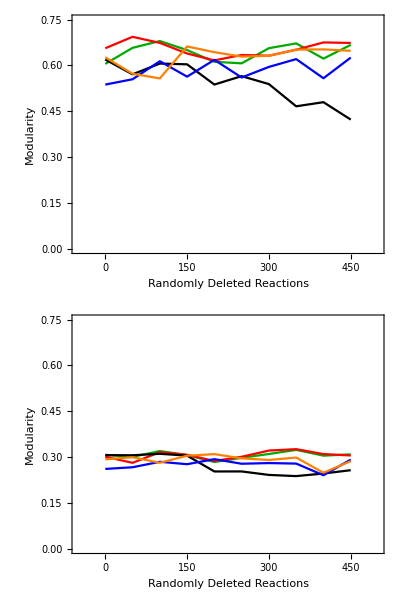
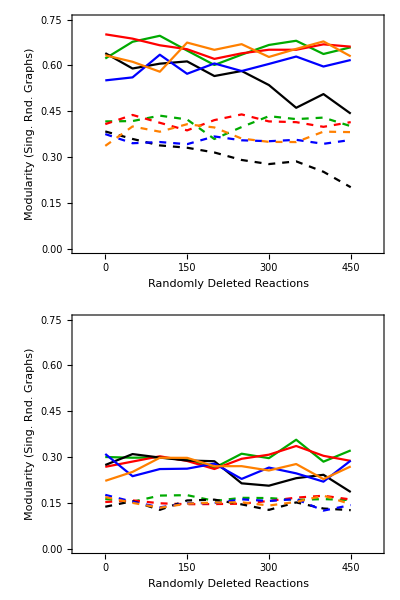
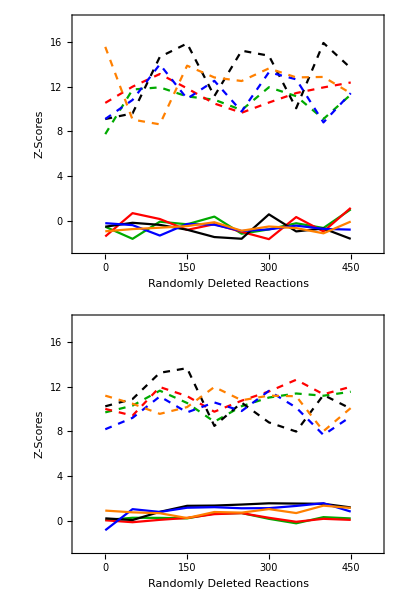

```mathematica
padding=38;
modularityplotrange={0,0.75};
xaxisplotrange={-50,500};
zscorerange={-2.5,18};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}]}]
,Column[{LineLegend[{Darker@Green,Red,Black,Blue,Orange},{"[-0.5,0.5] -> 105pcs","[-50,50] -> 105pcs","[-5,5] -> 105pcs","[-0.5,0.5] -> 210pcs","[-50,50] -> 210pcs"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Constrained\nBound Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

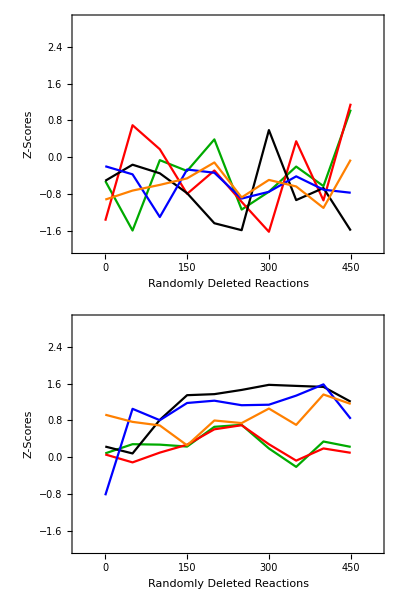

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```

Objective Function Interval: (2,4), bounds: {0.5, 5, 250}, term amounts: {105, 525}

Data Input

```mathematica
modularityvalues12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-modularityvalues-fss.mx"];
modularityvalues12m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-modularityvalues-fss.mx"];
modularityvalues12black=Import["plot_values/fxd_bounds/(2,4)-modularityvalues-fss.mx"];
modularityvalues12m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-modularityvalues-fss.mx"];
modularityvalues12p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-modularityvalues-fss.mx"];

modularityvalues32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-modularityvalues-fbs.mx"];
modularityvalues32m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-modularityvalues-fbs.mx"];
modularityvalues32black=Import["plot_values/fxd_bounds/(2,4)-modularityvalues-fbs.mx"];
modularityvalues32m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-modularityvalues-fbs.mx"];
modularityvalues32p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-modularityvalues-fbs.mx"];
```

```mathematica
singlerandomerdrenmodularityvalues12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12black=Import["plot_values/fxd_bounds/(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12black=Import["plot_values/fxd_bounds/(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-singrand-comm-modularityvalues-fss.mx"];
singlerandomerdrenmodularityvalues12p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-singrand-erd-modularityvalues-fss.mx"];
singlerandomcommmodularityvalues12p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-singrand-comm-modularityvalues-fss.mx"];

singlerandomerdrenmodularityvalues32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32black=Import["plot_values/fxd_bounds/(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32black=Import["plot_values/fxd_bounds/(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
singlerandomerdrenmodularityvalues32p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-singrand-erd-modularityvalues-fbs.mx"];
singlerandomcommmodularityvalues32p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-singrand-comm-modularityvalues-fbs.mx"];
```

```mathematica
zscores12m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-zscores-fss.mx"];
zscores12m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-zscores-fss.mx"];
zscores12black=Import["plot_values/fxd_bounds/(2,4)-zscores-fss.mx"];
zscores12m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-zscores-fss.mx"];
zscores12p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-zscores-fss.mx"];

zscores32m4p4=Import["plot_values/fxd_coeffs/-05+05_105_(2,4)-zscores-fbs.mx"];
zscores32m1p1=Import["plot_values/fxd_coeffs/-05+05_525_(2,4)-zscores-fbs.mx"];
zscores32black=Import["plot_values/fxd_bounds/(2,4)-zscores-fbs.mx"];
zscores32m2m4=Import["plot_values/fxd_coeffs/-5+5_525_(2,4)-zscores-fbs.mx"];
zscores32p2p4=Import["plot_values/fxd_coeffs/-250+250_525_(2,4)-zscores-fbs.mx"];
```

```mathematica
deletionrange=Range[0,450,50]
```

{0,50,100,150,200,250,300,350,400,450}

```mathematica
modularityvalues12={Thread[{deletionrange,modularityvalues12m4p4}],Thread[{deletionrange,modularityvalues12m1p1}],Thread[{deletionrange,modularityvalues12black}],Thread[{deletionrange,modularityvalues12m2m4}],Thread[{deletionrange,modularityvalues12p2p4}]};
modularityvalues32={Thread[{deletionrange,modularityvalues32m4p4}],Thread[{deletionrange,modularityvalues32m1p1}],
Thread[{deletionrange,modularityvalues32black}],Thread[{deletionrange,modularityvalues32m2m4}],Thread[{deletionrange,modularityvalues32p2p4}]};
```

```mathematica
singlerandommodularityvalues12={Thread[{deletionrange,singlerandomerdrenmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues12m1p1}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues12black}],
Thread[{deletionrange,singlerandomcommmodularityvalues12black}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues12m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues12p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues12p2p4}]};
singlerandommodularityvalues32={Thread[{deletionrange,singlerandomerdrenmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m4p4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m1p1}],Thread[{deletionrange,singlerandomcommmodularityvalues32m1p1}],
Thread[{deletionrange,singlerandomerdrenmodularityvalues32black}],
Thread[{deletionrange,singlerandomcommmodularityvalues32black}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomcommmodularityvalues32m2m4}],Thread[{deletionrange,singlerandomerdrenmodularityvalues32p2p4}],Thread[{deletionrange,singlerandomcommmodularityvalues32p2p4}]};
```

```mathematica
zscores12={Thread[{deletionrange,zscores12m4p4[[All,1]]}],Thread[{deletionrange,zscores12m4p4[[All,2]]}],Thread[{deletionrange,zscores12m1p1[[All,1]]}],Thread[{deletionrange,zscores12m1p1[[All,2]]}],
Thread[{deletionrange,zscores12black[[All,1]]}],
Thread[{deletionrange,zscores12black[[All,2]]}],
Thread[{deletionrange,zscores12m2m4[[All,1]]}],Thread[{deletionrange,zscores12m2m4[[All,2]]}],Thread[{deletionrange,zscores12p2p4[[All,1]]}],Thread[{deletionrange,zscores12p2p4[[All,2]]}]};
zscores32={Thread[{deletionrange,zscores32m4p4[[All,1]]}],Thread[{deletionrange,zscores32m4p4[[All,2]]}],Thread[{deletionrange,zscores32m1p1[[All,1]]}],Thread[{deletionrange,zscores32m1p1[[All,2]]}],Thread[{deletionrange,zscores32black[[All,1]]}],
Thread[{deletionrange,zscores32black[[All,2]]}],
Thread[{deletionrange,zscores32m2m4[[All,1]]}],Thread[{deletionrange,zscores32m2m4[[All,2]]}],Thread[{deletionrange,zscores32p2p4[[All,1]]}],Thread[{deletionrange,zscores32p2p4[[All,2]]}]};
```

Plots

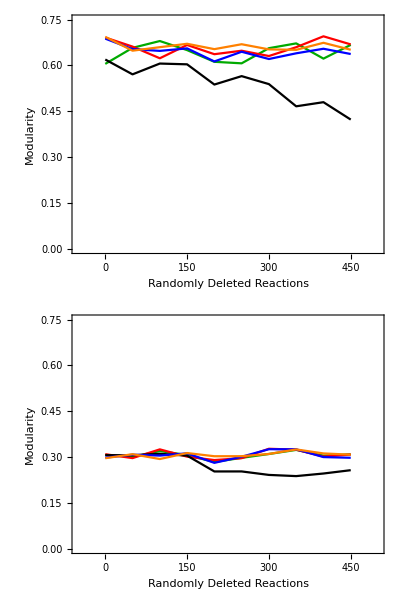
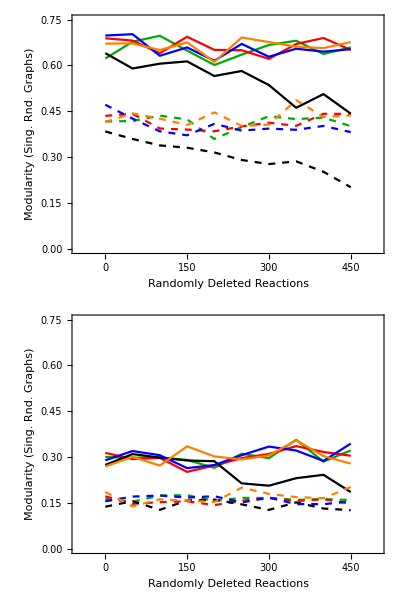
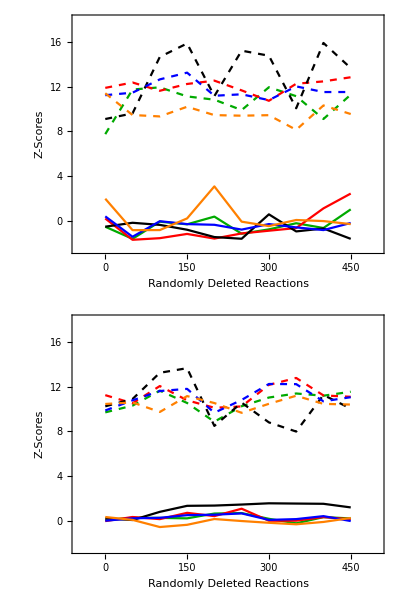

```mathematica
padding=38;
modularityplotrange={0,0.75};
xaxisplotrange={-50,500};
zscorerange={-2.5,18};
Row[{
Column[{ListLinePlot[modularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[modularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{"Randomly Deleted Reactions",None}},PlotStyle->{Darker@Green,Red,Black,Blue,Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],
Column[{ListLinePlot[singlerandommodularityvalues12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}],ListLinePlot[singlerandommodularityvalues32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,modularityplotrange}]}],Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,zscorerange}]}]
,Column[{LineLegend[{Darker@Green,Red,Black,Blue,Orange},{"[-0.5,0.5] -> 105pcs","[-0.5,0.5] -> 525pcs","[-5,5] -> 105pcs","[-5,5] -> 525pcs","[-250,250] -> 525pcs"},LegendLayout->"Column",LegendFunction->"Frame",LegendLabel->"Constrained\nBound Intervals",LegendMarkerSize->{20,20}],LineLegend[{Dashed,Black},{"Degrees Fixed\nNull Model","Modularity\nNull Model"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->{20,20}]}]}]
```

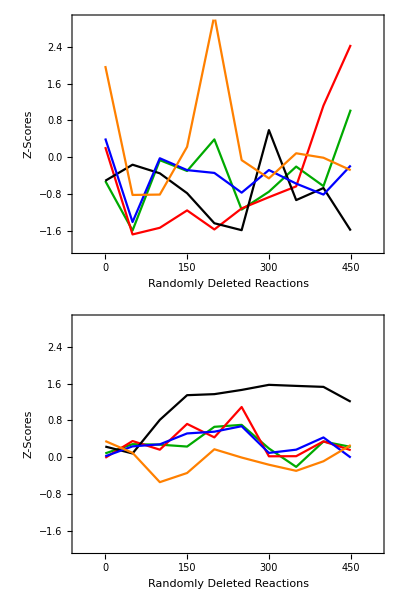

```mathematica
Column[{ListLinePlot[zscores12,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}],ListLinePlot[zscores32,Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-Scores",None},{"Randomly Deleted Reactions",None}},PlotStyle->{{Dashed,Darker@Green},Darker@Green,{Dashed,Red},Red,{Dashed,Black},Black,{Dashed,Blue},Blue,{Dashed,Orange},Orange},ImageSize->350,PlotRange->{xaxisplotrange,{-2,3}}]}]
```